TemporalData::rsmplng: 数据没有均匀间隔，并且将自动采样到最小时间增量的解决方案 .

TimeSeriesModel[…]

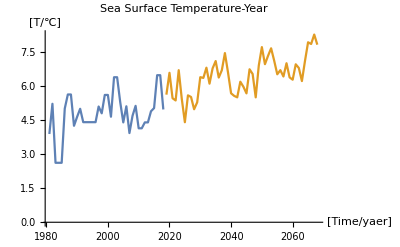

```mathematica
data1={{1981,3.89},{1982,5.22},{1983,2.62},{1986,5.01},{1987,5.63},{1989,4.25},{1990,4.64},{1991,5},{1992,4.41},{1997,5.1},{1998,4.8},{1999,5.61},{2001,4.65},{2002,6.39},{2004,5.3},{2005,4.4},{2006,5.11},{2007,3.93},{2008,4.69},{2009,5.13},{2010,4.14},{2012,4.4},{2014,4.89},{2015,5.03},{2016,6.48},{2018,4.97}};
tsm=TimeSeriesModelFit[data1,{"SARIMA",{{2,1,2},{6,0,2},5}}]
ListLinePlot[{tsm["TemporalData"],TimeSeriesForecast[tsm,{50}]},AxesLabel->{RawBoxes[RowBox[{"[",RowBox[{"Time","/","yaer"}],"]"}]],RawBoxes[RowBox[{"[",RowBox[{"T","/","℃"}],"]"}]]},PlotLabel->HoldForm[Sea Surface Temperature-Year],LabelStyle->{FontFamily->"Times New Roman",12,GrayLevel[0]}]
```

```mathematica
Do[Print[tsm[2017+10*n]],{n,1,5}]
```

5.5211

6.69876

6.53408

6.42263

8.27102

43.1096-0.568571 x

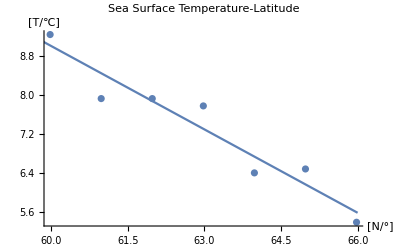

```mathematica
data2={{59.97917,9.23},{60.97917,7.92},{61.97917,7.92},{62.97917,7.77},{63.97917,6.4},{64.97917,6.48},{65.97917,5.39}};
n=Fit[data2,{1,x},x](*R^2=0.9194*)
Show[ListPlot[data2],Plot[n,{x,59,66}],AxesLabel->{RawBoxes[RowBox[{"[",RowBox[{"N","/","°"}],"]"}]],RawBoxes[RowBox[{"[",RowBox[{"T","/","℃"}],"]"}]]},PlotLabel->HoldForm[Sea Surface Temperature-Latitude],LabelStyle->{FontFamily->"Times New Roman",12,GrayLevel[0]}]
```

-4.95656×10^10+7.05086×10^8 x-4.01197×10^6 x^2+11414. x^3-16.2361 x^4+0.00923807 x^5

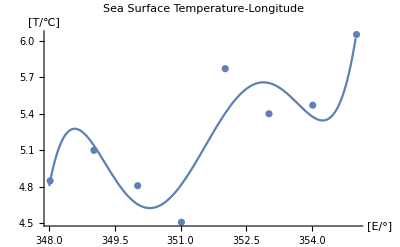

```mathematica
data3={{355.0208,6.05},{354.0208,5.47},{353.0208,5.4},{352.0208,5.77},{351.0208,4.51},{350.0208,4.81},{349.02084,5.1},{348.02084,4.85}};
w=Fit[data3,{1,x,x^2,x^3,x^4,x^5},x](*R^2=0.8282*)
Show[ListPlot[data3],Plot[w,{x,348,355}],AxesLabel->{RawBoxes[RowBox[{"[",RowBox[{"E","/","°"}],"]"}]],RawBoxes[RowBox[{"[",RowBox[{"T","/","℃"}],"]"}]]},PlotLabel->HoldForm[Sea Surface Temperature-Longitude],LabelStyle->{FontFamily->"Times New Roman",12,GrayLevel[0]}]
```

```mathematica
f=43.109585228571156-0.5685714285714245 x-4.9565597109171364*^10+7.050856750205353*^8 y-4.011970453856655*^6 y^2+11413.999841681154 y^3-16.23612188306266 y^4+0.009238065520264797 y^5
```

-4.95656×10^10-0.568571 x+7.05086×10^8 y-4.01197×10^6 y^2+11414. y^3-16.2361 y^4+0.00923807 y^5

```mathematica
Plot3D[f,{x,59,66},{y,348,355}]
```

-Graphics3D-

```mathematica
a[x_,y_]=-4.956559708399622*^10-0.5685714285714245 x+7.050856750205353*^8 y-4.011970453856655*^6 y^2+11413.999841681154 y^3-16.23612188306266 y^4+0.009238065520264797 y^5+tsm[2017];
a[59,355]
```

4.12775

```mathematica
Plot[{x=(a[59,355]-(-4.956559708399622*^10+7.050856750205353*^8 y-4.011970453856655*^6 y^2+11413.999841681154 y^3-16.23612188306266 y^4+0.009238065520264797 y^5+tsm[2017]))/(-0.568571),
x=(a[59,355]-(-4.956559708399622*^10+7.050856750205353*^8 y-4.011970453856655*^6 y^2+11413.999841681154 y^3-16.23612188306266 y^4+0.009238065520264797 y^5+tsm[2027]))/(-0.568571),x=(a[59,355]-(-4.956559708399622*^10+7.050856750205353*^8 y-4.011970453856655*^6 y^2+11413.999841681154 y^3-16.23612188306266 y^4+0.009238065520264797 y^5+tsm[2037]))/(-0.568571),x=(a[59,355]-(-4.956559708399622*^10+7.050856750205353*^8 y-4.011970453856655*^6 y^2+11413.999841681154 y^3-16.23612188306266 y^4+0.009238065520264797 y^5+tsm[2047]))/(-0.568571),x=(a[59,355]-(-4.956559708399622*^10+7.050856750205353*^8 y-4.011970453856655*^6 y^2+11413.999841681154 y^3-16.23612188306266 y^4+0.009238065520264797 y^5+tsm[2057]))/(-0.568571),x=(a[59,355]-(-4.956559708399622*^10+7.050856750205353*^8 y-4.011970453856655*^6 y^2+11413.999841681154 y^3-16.23612188306266 y^4+0.009238065520264797 y^5+tsm[2067]))/(-0.568571)},
{y,347,356},PlotLegends->{"2017","2027","2037","2047","2057","2067"},AxesLabel->{RawBoxes[RowBox[{"[",RowBox[{"E","/","°"}],"]"}]],RawBoxes[RowBox[{"[",RowBox[{"N","/","°"}],"]"}]]},PlotLabel->HoldForm[Latitude-Longitude],LabelStyle->{FontFamily->"Times New Roman",12,GrayLevel[0]}]
```

```mathematica
GeoGraphics[{EdgeForm[Black],FaceForm[Red],Polygon[LinguisticAssistant]},GeoRange->{{55,65},{-15,0}}]
```